# The Sandpile Model

Jonas Kaufman & Jon Ueki

## Introduction

The Sandpile Model, also known as the Bak-Tang-Wiesenfeld model, is a cellular automaton that aims to model...

## Graphics Setup

```mathematica
Module[{cmds= {"Plot", "ListPlot", "ListLinePlot", "ListLogPlot", "ListLogLogPlot","LogPlot","LogLogPlot","ListStepPlot"}},
For[j=1, j≤ Length[cmds],j++,SetOptions[Symbol[ cmds[[j]] ], Frame->True,LabelStyle->{Larger, FontFamily->"Utopia"}]]
]
```

## 1-D Model

The model takes place on a row representing half a sandpile where each cell has a slope z_n and height h_n where z_n=h_n-h_(n+1)......

### Initialization

The global variable row keeps track of the slope at each cell

```mathematica
length=20; (* length of row *)
zCrit1D=1;(* critical slope *)
randomRow[]:=row=Table[RandomInteger[zCrit],{length}] (* initialize row randomly *)
constantRow[c_]:=row=Table[c,{length}](* initialize row to constant slope *)
```

### Updating

relaxation1D relaxes the entire row until stable

```mathematica
relaxation1D[]:=Module[{i,stable=False},
While[!stable,
stable=True;
For[i=1,i≤ length,i++,
If[row[[i]]> zCrit1D,
stable=False;
If[1<i<length,row[[i]]-=2;row[[i+1]]++;row[[i-1]]++;];
If[i==1,row[[i]]-=2;row[[i+1]]++;];
If[i==length,row[[i]]--;row[[i-1]]++];
];
];
];
]
```

addGrain adds a grain of sand at a specific or random place

```mathematica
addGrain1D[] :=Module[{r},
r=RandomInteger[{1,length}];
row[[r]]++;
If[r>1,row[[r-1]]--]
];
```

pourSand adds numGrains grains of sand and relaxes after each

```mathematica
pourSand[numGrains_]:=Module[{n,rows={row}},
For[n=1,n≤numGrains,n++,
addGrain1D[];
relaxation1D[];
AppendTo[rows,row]; 
];
rows
]
```

### Simulation

If sand is added randomly to an empty row, the pile eventually reaches a critical state in which the slope at each cell is simply the critical slope.

```mathematica
constantRow[0];
rows=pourSand[600];
Animate[GraphicsColumn[{
ListStepPlot[Table[Total[rows[[t]][[i;;]]],{i,length}],FrameLabel->{"i","h"},PlotRange->{0,length*zCrit1D+1}],
ListStepPlot[rows[[t]],FrameLabel->{"i","z"},PlotRange->{-zCrit1D-1,zCrit1D+1}]
}],{t,1,Length[rows],1,Appearance->"Labeled"},AnimationRunning->False,AnimationRate->Automatic]
```

## 2-D Model

The model takes place on a grid...

#### Initialization

The global variable grid keeps track of the slope at each cell

```mathematica
gridSize = 20; (* side length of grid *)
zCrit = 2; (* the critical slope *)
randomGrid[]:=grid = Table[Table[RandomInteger[zCrit], {n, gridSize}], {n, gridSize}]; (* initialize grid randomly *)
constantGrid[c_]:=grid = Table[Table[c, {n, gridSize}], {n, gridSize}]; (* initialize grid to constant slope *)

avalancheFreq = Table[0, {n, 2 * gridSize^2}]; (*how many times an avalanche of a certain size occurs*)
avalancheTime = {}; (*The size of an avalanche when the nth grain of sand is dropped*)
```

#### Updating

relaxAll relaxes the entire grid until stable

```mathematica
relaxAll[]:=Module[{i,j,stable=False},
While[!stable,
stable=True;
For[i=1,i≤ gridSize,i++,
For[j=1,j≤ gridSize,j++,
If[grid[[i,j]]> zCrit,
stable=False;
(* remove slope *)
grid[[i,j]]-=2;
If[i≠ gridSize,grid[[i,j]]--];
If[j≠ gridSize,grid[[i,j]]--];
(* add slope to neighbors *)
If[i≠1,grid[[i-1,j]]++];
If[j≠1,grid[[i,j-1]]++];
If[i≠gridSize,grid[[i+1,j]]++];
If[j≠gridSize,grid[[i,j+1]]++];
];
];
];
];
]
```

update relaxes a single cell and it’s neighbors (then their neighbors, etc.) until stable

```mathematica
update[ii_,jj_]:=Module[{stable=False,look={{ii,jj}},l,i,j},
While[!stable,
stable=True;
For[l=1,l≤ Length[look],l++,
{i,j}=look[[l]];
If[grid[[i,j]]>zCrit,
stable=False;
s++; (* count topple *)
(* remove slope *)
grid[[i,j]]-=2;
If[i≠ gridSize,grid[[i,j]]--];
If[j≠ gridSize,grid[[i,j]]--];
(* add slope to neighbors *)
If[i≠1,grid[[i-1,j]]++];
If[j≠1,grid[[i,j-1]]++];
If[i≠gridSize,grid[[i+1,j]]++];
If[j≠gridSize,grid[[i,j+1]]++];
(* relax neighbors *)
If[i≠1,AppendTo[look,{i-1,j}]];
If[j≠1,AppendTo[look,{i,j-1}]];
If[i≠gridSize,AppendTo[look,{i+1,j}]];
If[j≠gridSize,AppendTo[look,{i,j+1}]];
];
];
];
]
```

addSand adds a grain of sand at a specific or random place

```mathematica
addGrain[random_,place_] :=Module[{i, j}, 
If[random,(*If we activate random, then add grains randomly*)
i=RandomInteger[{1,gridSize}];j=RandomInteger[{1,gridSize}];,
i=place[[1]];j=place[[2]];
];
grid[[i,j]]+=2;
If[j≠1,grid[[i,j-1]]--];
If[i≠1,grid[[i-1,j]]--];
update[i,j];
]
```

run adds totalSand_ grains of sand and relaxes after each
returns a list of the total number of topples each time step

```mathematica
run[totalSand_, random_:False,place_:{1,1}] := Module[{n,T,sList={},TList={}},
For[n=1,n≤ totalSand,n++,
s=0;
addGrain[random,place];
AppendTo[sList,s];
AppendTo[avalancheTime, s];
avalancheFreq[[s+1]]++;
];
sList
]
```

#### Statistics

Distribution of slopes

```mathematica
slopeDist[]:= Module[{slopes, slopedist = {}, i, j},
slopes = Table[0, {n, 0, zCrit}];
For[i=1, i≤ gridSize, i++,
For[j=1, j≤gridSize,j++,
slopes[[grid[[i,j]] + 1]]++;
];
];
(*make x-coordinate and y-coordinate pair *)
For[i=1, i≤Length[slopes], i++,
AppendTo[slopedist, {i-1, slopes[[i]]}];
];
slopedist
]
```

sDist produces a distribution of avalanche sizes from a list of avalanche sizes at each time step

```mathematica
sDist[sList_]:=Module[{dist=Table[0,{Max[sList]}],s,t},
For[t=1,t≤ Length[sList],t++,
s=sList[[t]];
If[s≠0,
dist[[s]]++
];
];
1./Length[sList] dist
]
```

#### Visualization

heights calculates an array of heights based on an array of slopes

```mathematica
heights[grid_]:=Module[{i,j,gridSize=Length[grid],heights},
heights=Table[Table[0, {gridSize}], {gridSize}];
For[i=gridSize-1,i> 0,i--,
For[j=gridSize-1,j> 0,j--,
heights[[i,j]]= 0.5(grid[[i,j]]+heights[[i+1,j]]+heights[[i,j+1]]);
];
];
heights
]
```

heightFull calculates an array of heights for the full sandpile based on one quarter of it

```mathematica
heightsFull[grid_]:=Module[{i,j,h,gridSize=Length[grid],heights},
heights=Table[Table[0, {n, 2*gridSize}], {n, 2*gridSize}];
For[i=gridSize-1,i≥0,i--,
For[j=gridSize-1,j≥0,j--,
h=0.5(If[i==0 || j==0,grid[[i+1,j+1]] ,grid[[i,j]]]
+ heights[[i+1 + gridSize,j + gridSize]]
+heights[[i + gridSize,j+1 + gridSize]]);
heights[[gridSize+i,gridSize+j]]=h;
heights[[gridSize+i, gridSize - j]] =h;
heights[[gridSize-i, gridSize+j]] = h;
heights[[gridSize-i, gridSize - j]] = h;
];
];
heights
]
```

#### Run and Plot the Simulation

```mathematica
constantGrid[10];
```

```mathematica
relaxAll[];
```

```mathematica
sList=run[100000, True];
```

```mathematica
(*Dynamic[GraphicsRow[{ArrayPlot[grid,PlotLegends->Automatic,ColorFunction->GrayLevel],
ArrayPlot[heights[grid],PlotLegends->Automatic,ColorFunction->GrayLevel]},
ImageSize->Large,AspectRatio->3/4]]*)
```

```mathematica
ListPlot3D[heightsFull[grid],InterpolationOrder->1, Mesh->None,ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
ListPlot[sList,PlotRange->All,Filling->Axis]
```

$Aborted

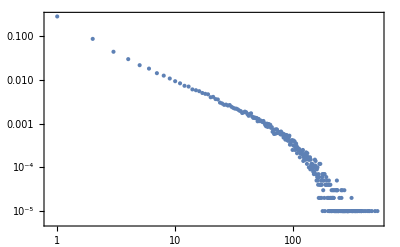

```mathematica
ListLogLogPlot[sDist[sList]]
```

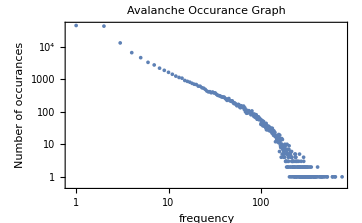

```mathematica
Show[ListLogLogPlot[avalancheFreq],AxesLabel->{HoldForm[frequency],HoldForm[Number of occurances]},PlotLabel->HoldForm[Avalanche Occurance Graph],LabelStyle->{14,GrayLevel[0]}]
```

```mathematica
FindFit[sDist[sList],a*x^b,{a,b},x]
```

{a→0.280404,b→-1.60087}